```mathematica
(* ClearAll["Global`*"] *)
```

```mathematica
checkPaperLink[link_,bibcode_]:=Quiet[And[StringTake[link,35]=="https://ui.adsabs.harvard.edu/#abs/" ,StringTake[link,-9]=="/abstract",StringTake[link,{36,-10}]!=bibcode]]

getPaperLinks[session_,bibcode_]:=
(
Pause[1];(*pause for 1 seconds to let JavaScript run*)
links001=WebExecute[session,"PageHyperlinks"];
links002=DeleteDuplicates@links001;
links003=Select[links002,checkPaperLink[#,bibcode]&]
)

(* getPaperLinks[session,bibcode] *)
```

```mathematica
getPapersOnePageAndNext[session_,bibcode_]:=
(
paperLinks=getPaperLinks[session,bibcode];
hyperLinkObjects=WebExecute[session,"LocateElements"->"Tag"->"a"];
textList=WebExecute["ElementText"->hyperLinkObjects];
If[MemberQ[textList,"prev"] (* to prevent error that the paper have no reference *),
(
prevPosi=First@First@Position[textList,"prev"];
nextPosi=First@First@Position[textList,"next"];
),
(
prevPosi={};
nextPosi={};
)];
prevButton=hyperLinkObjects[[prevPosi]];
nextButton=hyperLinkObjects[[nextPosi]];
WebExecute["ElementText"->prevButton];
WebExecute["ElementText"->nextButton];
msg=WebExecute["ClickElement"->nextButton];
msgSuccessType=Head@msg;
output={paperLinks,msgSuccessType}
)

(* getPapersOnePageAndNext[session,bibcode] *)
```

```mathematica
getPapersMultiPage[session_,bibcode_]:=
(
{paperLinks,msgSuccessType}=getPapersOnePageAndNext[session,bibcode];
paperLinksAll=paperLinks;
While[(ToString@msgSuccessType=="Success"),
(
{paperLinks,msgSuccessType}=getPapersOnePageAndNext[session,bibcode];
paperLinksAll=Join[paperLinksAll,paperLinks];
)
];
paperLinksAll
);

(* getPapersMultiPage[session,bibcode] *)
```

```mathematica
getBibcode[url_,type_]:=
(
(* Type 1 is for (/abs/,/reference) , while Type 2 is for (/#abs/,/abstract)*)
If[type==1,
StringTake[url,{35,-12}],
If[type==2,
StringTake[url,{36,-10}],
"else"
]
]
);

arXiv2RefBibcodes[arXivID_]:=
(
session=StartWebSession[Visible->Not@headlessSwitch];
linkPrefix="https://ui.adsabs.harvard.edu/abs/arXiv:";
linkSuffix="/references";
myLink=StringJoin[linkPrefix,arXivID,linkSuffix]; 
WebExecute[session,"OpenPage"->myLink];
Pause[4];(*pause for 3 seconds to let JavaScript run*)
url001=WebExecute[session,"PageURL"];

(* get the meta data of the paper*)
bibcode=getBibcode[url001,1];
headers=WebExecute[session,"LocateElements"->"Tag"->"h2"];
headersText=WebExecute["ElementText"->headers];
paperTitle=headersText[[-1]];

(* get the reference of the paper*)
paperLinksAll=DeleteDuplicates@getPapersMultiPage[session,bibcode] ;
DeleteObject[session];
bibcodesRef=getBibcode[#,2]&/@paperLinksAll;
output={{bibcode,paperTitle},bibcodesRef}
)

(* arXivID="1609.05206"; *)
(* arXiv2RefBibcodes[arXivID] *)
```

```mathematica
breakString[stringIn_]:=
(
nextLine="\n";
stSegments=Flatten@NestWhile[
(
lastString=Last[#];
lastFront=StringTake[lastString,{1,10}];
lastBack=StringTake[lastString,{11,-1}];
initialCheck=Length@#;
If[initialCheck==1,firstString={},firstString=First@#];
firstStringNew=Join[firstString,{lastFront}];
{firstStringNew,lastBack}
)&
,{stringIn},StringLength@Last[#]≥11&];
stBreak=StringJoin[Riffle[stSegments,nextLine]]
);
```

Part I

Progress: 1 out of 24

Progress: 2 out of 24

Progress: 3 out of 24

Progress: 4 out of 24

Progress: 5 out of 24

Progress: 6 out of 24

Progress: 7 out of 24

Progress: 8 out of 24

Progress: 9 out of 24

Progress: 10 out of 24

Progress: 11 out of 24

Progress: 12 out of 24

Progress: 13 out of 24

Progress: 14 out of 24

Progress: 15 out of 24

Progress: 16 out of 24

Progress: 17 out of 24

Part::partd: Part specification $Failed⟦-1⟧ is longer than depth of object.

Progress: 18 out of 24

Progress: 19 out of 24

Progress: 20 out of 24

Progress: 21 out of 24

Progress: 22 out of 24

Progress: 23 out of 24

Progress: 24 out of 24

Part II

Part III

Part IV

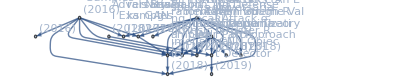

```mathematica
(* Main program run start from here *)
nbDir=NotebookDirectory[];
headlessSwitch=True; (* If headlessSwitchc = False, then you will see the Browser pop up when doing web-scrapping*)
{arXivIDLists,yearLists}=Import[StringJoin[nbDir,"arXivIDandYearLists.mx"]];

numPapers=Length@arXivIDLists;

(* Get all papers' bibcodes and respective references' bibcodes*)
Print["Part I"];
i=1;
myBibcodesAll={};
relationahipAll={};
paperNameRelationshipAll={};
yearRelationshipAll={};

While[i<=numPapers,
(
Print[StringJoin["Progress: ",ToString[i]," out of ",ToString[numPapers]]];
arXivID=arXivIDLists[[i]];
yearI=yearLists[[i]];
{{myBibcode,paperTitle},bibcodesRef}=arXiv2RefBibcodes[arXivID];
paperTitle=ToString@paperTitle;
myBibcodesAll=Join[myBibcodesAll,myBibcode];
relationahipAll=Join[relationahipAll,{{myBibcode,bibcodesRef}}];
paperNameRelationshipAll=Join[paperNameRelationshipAll,{myBibcode->paperTitle}];
yearRelationshipAll=Join[yearRelationshipAll,{myBibcode->yearI}]

);
i++];

(* remove all references that is not in the original paper list *)
Print["Part II"];
i=1;
mappingAll={};
While[i<=numPapers,
(
{myBibcode,bibcodesRef}=relationahipAll[[i]];
bibcodesRef=Select[bibcodesRef,MemberQ[myBibcodesAll,#]&];
mappingAll=Join[mappingAll,(#->myBibcode)&/@bibcodesRef];
);
i++];

(* remove some singleton papers from paperNameRelationshipAll as they don't appear in mappingAll, i.e. to avoid error of Graph[] *)
Print["Part III"];
parentPapers=First/@mappingAll;
childPapers=Last/@mappingAll;
parentChildPapers=Union[parentPapers,childPapers];
paperNameRelationshipAll=Select[paperNameRelationshipAll,MemberQ[parentChildPapers,First@#]&];
yearRelationshipAll=Select[yearRelationshipAll,MemberQ[parentChildPapers,First@#]&];


Print["Part IV"];
(* Break paper titles in lines and draw Graph *)
breakStrings=breakString/@(Last/@paperNameRelationshipAll);
breakStrings=MapThread[StringJoin[#1,"\n(",ToString@#2,")"]&,{breakStrings,(Last/@yearRelationshipAll)}];
paperNameRelationshipAllBreak=MapThread[(First[#1]->#2)&,{paperNameRelationshipAll,breakStrings}];
Graph[mappingAll,VertexLabels->paperNameRelationshipAllBreak,GraphLayout->"LayeredDigraphEmbedding"]
```